Example1

Consider a vector field

```mathematica
X = {x,y +x};
```

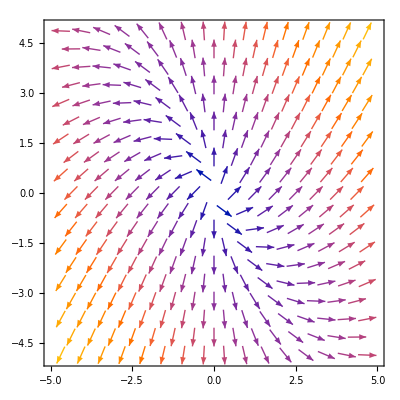

```mathematica
VectorPlot[X,{x,-5,5},{y,-5,5}]
```

To find the integral curve we solve the differential equation with different initial conditions

```mathematica
soln1=Flatten[DSolve[{x'[t]==x[t],y'[t]==x[t]+y[t], x[0]==-1/2, y[0]==1/2 },{x[t],y[t]},{t}]]//FullSimplify
```

{x[t]→-ⅇ^t/2,y[t]→-1/2 ⅇ^t (-1+t)}

```mathematica
soln2=Flatten[DSolve[{x'[t]==x[t],y'[t]==x[t]+y[t], x[0]==1/2, y[0]==1/2 },{x[t],y[t]},{t}]]//FullSimplify
```

{x[t]→ⅇ^t/2,y[t]→1/2 ⅇ^t (1+t)}

```mathematica
soln3=Flatten[DSolve[{x'[t]==x[t],y'[t]==x[t]+y[t], x[0]==1/2, y[0]==-1/2 },{x[t],y[t]},{t}]]//FullSimplify
```

{x[t]→ⅇ^t/2,y[t]→1/2 ⅇ^t (-1+t)}

```mathematica
soln4=Flatten[DSolve[{x'[t]==x[t],y'[t]==x[t]+y[t], x[0]==-1/2, y[0]==-1/2 },{x[t],y[t]},{t}]]//FullSimplify
```

{x[t]→-ⅇ^t/2,y[t]→-1/2 ⅇ^t (1+t)}

```mathematica
Animate[Show[VectorPlot[X,{x,-5,5},{y,-5,5},VectorColorFunction->None],
ParametricPlot[soln1[[All,2]],{t,0,t0},PlotRange->{{-5,5},{-5,5}},PlotStyle->Red],
ParametricPlot[soln2[[All,2]],{t,0,t0},PlotRange->{{-5,5},{-5,5}},PlotStyle->Green],
ParametricPlot[soln3[[All,2]],{t,0,t0},PlotRange->{{-5,5},{-5,5}},PlotStyle->Orange],
ParametricPlot[soln4[[All,2]],{t,0,t0},PlotRange->{{-5,5},{-5,5}},PlotStyle->Black]],{t0,0,5}]
```

```mathematica
Quit[]
```

Example2

Consider a vector field in R^3:

```mathematica
X = {y, -z, x};
```

```mathematica
VectorPlot3D[X,{x,-5,5},{y,-5,5},{z,-5,5}]
```

-Graphics3D-

To find the integral curve, we solve the following differential equations with the initial condition that (x,y,z) at t=0 is (1,1,1)

```mathematica
soln=Flatten[DSolve[{x'[t]==y[t],y'[t]==-z[t], z'[t]==x[t], x[0]==1, y[0]==1, z[0]==1 },{x[t],y[t],z[t]},{t}]]//FullSimplify
```

{x[t]→1/3 ⅇ^-t (-1+4 ⅇ^(3 t/2) Cos[(√3 t)/2]),y[t]→1/3 ⅇ^-t (1+2 ⅇ^(3 t/2) (Cos[(√3 t)/2]-√3 Sin[(√3 t)/2])),z[t]→1/3 ⅇ^-t (1+2 ⅇ^(3 t/2) (Cos[(√3 t)/2]+√3 Sin[(√3 t)/2]))}

```mathematica
Show[ParametricPlot3D[soln[[All,2]],{t,0,100},PlotRange->{{-50,50},{-50,50},{-50,50}},PlotPoints->25,MaxRecursion->10],
VectorPlot3D[X,{x,-50,50},{y,-50,50},{z,-50,50},VectorPoints->Coarse]]
```

-Graphics3D-